## This notebook generates the dS symmetric states for Einstein+Scalar with the ϕM, ϕQ model of 1805.01806

## Select model parameters

```mathematica
smodel={ϕM->62/100,ϕQI-> 1/10, H-> 1};
eϵ0=6;
eϵ1=5;
ϵ0=10^(-eϵ0);
ϵ1=10^(-eϵ1);
fileMetricfunction="mf_phiM_"<>ToString[N[ϕM/.smodel]]<>"_ϕQ_"<>ToString[1/ϕQI/.smodel]<>"_dat.m";
fileVacdata="vd_phiM_"<>ToString[N[ϕM/.smodel]]<>"_ϕQ_"<>ToString[1/ϕQI/.smodel]<>"_e0_"<>ToString[eϵ0]<>"_e1_"<>ToString[eϵ1]<>"_dat.m";
```

### Potential. Computes the minium of the potential, ϕE

```mathematica
(*Super Potential*)
WW[ϕ_]:=-3/2-ϕ^2/2-ϕ^4/4/ϕM^2+ϕ^6 ϕQI
VV[ϕ_]:=-4/3 WW[ϕ]^2+1/2 WW'[ϕ]^2
sV=V-> Function[x,VV[x]];
ϕE=x/.FindRoot[VV'[x]==0/.smodel,{x,2.5}]

ϕEHP=x/.FindRoot[VV'[x]==0/.smodel,{x,25/10},WorkingPrecision->50]
SetDirectory[NotebookDirectory[]];
```

2.16588

2.1658827292071926130329191102154486480884715052243

## Equations (without derivation)

```mathematica
(*Einstein plus Klein Gordon equation*)
Ets={-2 ϕ0'[u]^2-(3 (2 S'[u]+u S''[u]))/(u S[u]),-V'[ϕ0[u]]+u^2 (-3 H+u^2 A'[u]+u A[u] (2+(3 u S'[u])/S[u])) ϕ0'[u]+u^4 A[u] ϕ0''[u],-(3 u^2 A[u] S'[u]^2)/S[u]^2-(2 V[ϕ0[u]]+u^4 A[u] ϕ0'[u]^2)/u^2-(3 ((-6 H+4 u A[u]+u^2 A'[u]) S'[u]+2 u^2 A[u] S''[u]))/(2 S[u]),1/2 ⅇ^(2 H t) (2 u^4 A[u] S'[u]^2+S[u]^2 (4 V[ϕ0[u]]+u^3 (2 A'[u]+2 u A[u] ϕ0'[u]^2+u A''[u]))+4 u^2 S[u] ((-3 H+2 u A[u]+u^2 A'[u]) S'[u]+u^2 A[u] S''[u])),-1/(2 S[u]^2)(6 u^4 A[u]^2 S'[u]^2+S[u]^2 (4 A[u] V[ϕ0[u]]+3 H (2 H+u^2 A'[u])+2 u^4 A[u]^2 ϕ0'[u]^2)+3 u^2 A[u] S[u] ((-8 H+4 u A[u]+u^2 A'[u]) S'[u]+2 u^2 A[u] S''[u]))};
```

```mathematica
(*These equations can be manipulated to get*)
EtsSs=3/2 H (-2 H-u^2 A'[u]+(2 u^2 A[u] S'[u])/S[u]);
(*Its solution is *)
Satn=S->Function[x,√A[x] Exp[H ∫_0^x 1/(A[y] y^2)ⅆy]];
```

```mathematica
(*Reduction to three dependent equations equation. One of them can be obtained form the other two*)
(*Equation E3 imply that A=1/u^2... *)
E1= V[ϕ0[u]]-(12 H^2-3 u^4 A'[u]^2+2 u^4 A[u]^2 ϕ0'[u]^2)/(4 A[u]);
E2=-(-12 H^2-12 u^3 A[u] A'[u]+3 u^4 A'[u]^2-8 u^4 A[u]^2 ϕ0'[u]^2)/(6 u^4 A[u])+A''[u];
E3=-V'[ϕ0[u]]+5/2 u^4 A'[u] ϕ0'[u]+u^3 A[u] (2 ϕ0'[u]+u ϕ0''[u]);
```

```mathematica
(*Equations in te form of 2403.14763.*)
ER1=(2 S'[u])/u+2/3 S[u] ϕ0'[u]^2+S''[u];
ER2=-V'[ϕ0[u]]/(u^4 A[u])+(2/u-(3 H)/(u^2 A[u])+A'[u]/A[u]+(3 S'[u])/S[u]) ϕ0'[u]+ϕ0''[u];
ER3=-(2 H^2)/(u^4 A[u])+(8 V[ϕ0[u]])/(3 u^4)-(4 H S'[u])/(u^2 S[u])+A'[u] (2/u-H/(u^2 A[u])+(3 S'[u])/S[u])+A''[u];
ER4=-(6 H)/u^2+A'[u]+(2 A[u] S'[u])/S[u]+(2 S[u] ((2 V[ϕ0[u]])/u^4-A[u] ϕ0'[u]^2))/(3 S'[u]);
```

```mathematica
(*series solutions close to the boundary*)
sNBs={A->Function[x,1/x^2 (1+Sum[x^(i)(a[i] + al[i] Log[x]) ,{i,1,7}]+ O[x]^5)],ϕ0-> Function[x,Λ x +x Sum[(phi[ i] + phil[i] Log[x]) x^(i),{i,1,7}]+O[x]^5]};
spsb[4]={a[2]->1/12 (-12 H^2-8 Λ^2+3 a[1]^2),a[3]->0,a[4]->1/54 (21 H^2 Λ^2+8 Λ^4+9 Λ^2 a[1]^2-36 Λ phi[2]),a[5]->1/54 (-3 H^2 Λ^2 a[1]-8 Λ^4 a[1]-9 Λ^2 a[1]^3+36 Λ a[1] phi[2]),a[6]->-1/(1800 ϕM^4)(300 Λ^6-200 Λ^6 ϕM^2-1512 H^4 Λ^2 ϕM^4-276 H^2 Λ^4 ϕM^4-80 Λ^6 ϕM^4-1200 Λ^6 ϕM^4 ϕQI+117 H^2 Λ^2 ϕM^4 a[1]^2-270 Λ^4 ϕM^4 a[1]^2-180 Λ^2 ϕM^4 a[1]^4+432 H^2 Λ ϕM^4 phi[2]+280 Λ^3 ϕM^4 phi[2]+540 Λ ϕM^4 a[1]^2 phi[2]+720 ϕM^4 phi[2]^2),al[1]->0,al[2]->0,al[3]->0,al[4]->-2/3 H^2 Λ^2,al[5]->2/3 H^2 Λ^2 a[1],al[6]->1/90 (-108 H^4 Λ^2-14 H^2 Λ^4-27 H^2 Λ^2 a[1]^2-72 H^2 Λ phi[2]),phi[1]->-1/2 Λ a[1],phi[3]->1/4 (-2 H^2 Λ a[1]+Λ a[1]^3-6 a[1] phi[2]),phi[4]->-1/(432 ϕM^4)(-162 Λ^5+108 Λ^5 ϕM^2+594 H^4 Λ ϕM^4+156 H^2 Λ^3 ϕM^4+56 Λ^5 ϕM^4+648 Λ^5 ϕM^4 ϕQI-216 H^2 Λ ϕM^4 a[1]^2+117 Λ^3 ϕM^4 a[1]^2+135 Λ ϕM^4 a[1]^4-648 H^2 ϕM^4 phi[2]-468 Λ^2 ϕM^4 phi[2]-648 ϕM^4 a[1]^2 phi[2]),phil[1]->0,phil[2]->H^2 Λ,phil[3]->-3/2 H^2 Λ a[1],phil[4]->1/12 (36 H^4 Λ+13 H^2 Λ^3+18 H^2 Λ a[1]^2)};

Snbps=Assuming[u>0, (Sqrt[A[u]]/.sNBs/.spsb[4]) Simplify[Exp[H Integrate[1/((A[u] u^2 /.sNBs/.spsb[4]) ),u]]]];
```

```mathematica
(*Near Horizon*)
sNHs={A->Function[x,∑_(i=1)^4 (x-1)^i (-1)^i ah[i]] ,ϕ0->Function[x,ϕh+∑_(i=1)^4 phih[i] (1-x)^i ]};
spsH[3]={ah[1]->2 H,ah[2]->1/3 (6 H-V[ϕh]),ah[3]->(2 (225 H^2-75 H V[ϕh]-4 V'[ϕh]^2))/(225 H),ah[4]->-(-9450 H^3+4725 H^2 V[ϕh]+504 H V'[ϕh]^2+16 V[ϕh] V'[ϕh]^2+18 V'[ϕh]^2 V''[ϕh])/(4725 H^2),phih[1]->V'[ϕh]/(5 H),phih[2]->(V'[ϕh] (42 H+5 V[ϕh]+3 V''[ϕh]))/(210 H^2)};
SnHps= (Normal[(Sqrt[A[1-ϵ]]/.sNHs/.spsH[3])Exp[Integrate[H(1/A[u]/u^2/.sNHs/.spsH[3]/.u-> 1-ϵ)  + O[ϵ,0]^6,ϵ]]]/.ϵ-> 1-u) + O[u,1]^3//Simplify;
```

```mathematica
SnHps= (Normal[(Sqrt[A[1-ϵ]]/.sNHs/.spsH[3])Exp[-Integrate[H(1/A[u]/u^2/.sNHs/.spsH[3]/.u-> 1-ϵ)  + O[ϵ,0]^6,ϵ]]]/.ϵ-> 1-u) + O[u,1]^5//Simplify;
```

## Numeric solver (uses 3 second order equations for A, S, and phi) (they are call ER1, ER2, ER3)

```mathematica
(*Solver*)
gsR[ϕH_,ϵh_,ϵb_]:=Module[{IC,ts},
IC={S[1-ϵh]==Normal[SnHps]/.u-> 1-ϵh/.sV/.smodel/.ϕh-> ϕH,S'[1-ϵh]==D[Normal[SnHps],u]/.u-> 1-ϵh/.sV/.smodel/.ϕh-> ϕH,A[1-ϵh]==Normal[A[1-ϵh]/.sNHs/.spsH[3]/.sV/.smodel/.ϕh-> ϕH],A'[1-ϵh]==Normal[A'[1-ϵh]/.sNHs/.spsH[3]/.sV/.smodel/.ϕh-> ϕH],ϕ0[1-ϵh]==Normal[ϕ0[1-ϵh]/.sNHs/.spsH[3]/.sV/.smodel/.ϕh-> ϕH],ϕ0'[1-ϵh]==Normal[ϕ0'[1-ϵh]/.sNHs/.spsH[3]/.sV/.smodel/.ϕh-> ϕH]}/.{phih[3]-> 0, phih[4]-> 0};
ts=Union[{ER1==0,ER2==0,ER3==0},
IC]/.sV/.smodel;
NDSolve[ts,{A,ϕ0,S},{u,ϵb,1-ϵh}]
]
```

```mathematica
(*Extraction of parameters*)
gVacuaParam[ϕMv_,ϵh_,ϵb_]:= Module[{param,ff,ns,data,fval,stest},
ns=gsR[ϕMv,ϵh,ϵb][[1]];
ff=Normal[ ϕ0[u]/.sNBs/.spsb[4]/.smodel];
param={Λ,a[1],phi[2]};
data=Table[{ϵb+ i ϵb,ϕ0[ϵb+i ϵb]}/.ns,{i,1,100}];
fval=FindFit[data,ff,param,u];
stest=Normal[Snbps/.smodel/.spsb[4]/.fval]/.u-> ϵb;
{Λ,a[1],phi[2],Sqrt[2]stest/S[ϵb]}/.ns/.fval
]
```

```mathematica
(*Solver that gives the metric functions with correct boundary conditions*)
gMetricFunction[ϕMv_,ϵh_,ϵb_]:= Module[{param,ff,ns,data,fval,stest,SS},
ns=gsR[ϕMv,ϵh,ϵb][[1]];
ff=Normal[ ϕ0[u]/.sNBs/.spsb[4]/.smodel];
param={Λ,a[1],phi[2]};
data=Table[{ϵb+ i ϵb,ϕ0[ϵb+i ϵb]}/.ns,{i,1,100}];
fval=FindFit[data,ff,param,u];
stest=Normal[Snbps/.smodel/.spsb[4]/.fval]/.u-> ϵb;
SS=S[ϵb]/stest/.ns/.fval;
{ns[[1]],ns[[2]],S-> Function[x,(S[x]/SS/.ns)]}
]
```

```mathematica
(*High Precission Solvers*)
gsRHP[ϕH_,ϵh_,ϵb_]:=Module[{IC,ts},
IC={S[1-ϵh]==Normal[SnHps]/.u-> 1-ϵh/.sV/.smodel/.ϕh-> ϕH,S'[1-ϵh]==D[Normal[SnHps],u]/.u-> 1-ϵh/.sV/.smodel/.ϕh-> ϕH,A[1-ϵh]==Normal[A[1-ϵh]/.sNHs/.spsH[3]/.sV/.smodel/.ϕh-> ϕH],A'[1-ϵh]==Normal[A'[1-ϵh]/.sNHs/.spsH[3]/.sV/.smodel/.ϕh-> ϕH],ϕ0[1-ϵh]==Normal[ϕ0[1-ϵh]/.sNHs/.spsH[3]/.sV/.smodel/.ϕh-> ϕH],ϕ0'[1-ϵh]==Normal[ϕ0'[1-ϵh]/.sNHs/.spsH[3]/.sV/.smodel/.ϕh-> ϕH]}/.{phih[3]-> 0, phih[4]-> 0};
ts=Union[{ER1==0,ER2==0,ER3==0},
IC]/.sV/.smodel;
NDSolve[ts,{A,ϕ0,S},{u,ϵb,1-ϵh},AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->30,MaxSteps->20000]
]
(*Extraction of parameters*)
gVacuaParamHP[ϕMv_,ϵh_,ϵb_]:= Module[{param,ff,ns,data,fval,stest},
ns=gsRHP[ϕMv,ϵh,ϵb][[1]];
ff=Normal[ ϕ0[u]/.sNBs/.spsb[4]/.smodel];
param={Λ,a[1],phi[2]};
data=Table[{ϵb+ i ϵb,ϕ0[ϵb+i ϵb]}/.ns,{i,1,100}];
(*fval=NonlinearModelFit[data,ff,param,u];
fval["BestFit"]*)
fval=FindFit[data,ff,param,u];
stest=Normal[Snbps/.smodel/.spsb[4]/.fval]/.u-> ϵb;
{Λ,a[1],phi[2],Sqrt[2]stest/S[ϵb]}/.ns/.fval
]
```

```mathematica
Npoints=1000;
ϕHtable[i_]:= ϕE(1-10^(-0.05- i/Npoints 11 ))
```

```mathematica
vacdata=Table[{ϕHtable[i],gVacuaParam[ϕHtable[i],ϵ1,ϵ0]},{i,0,Npoints}];
```

```mathematica
(*Export[fileVacdata,vacdata]*)
```

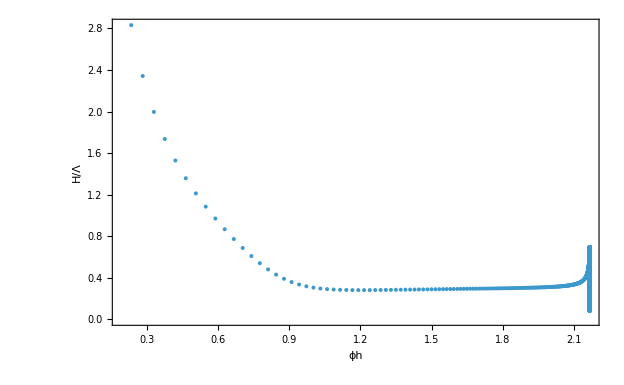

```mathematica
ListPlot[vacdata/.{ϕh_,{Λ_,a1_,phi2_,Σ_}}:> {ϕh,1/Λ},PlotRange-> Full,Frame-> True,FrameLabel->{ϕh,H/Λ}]
```

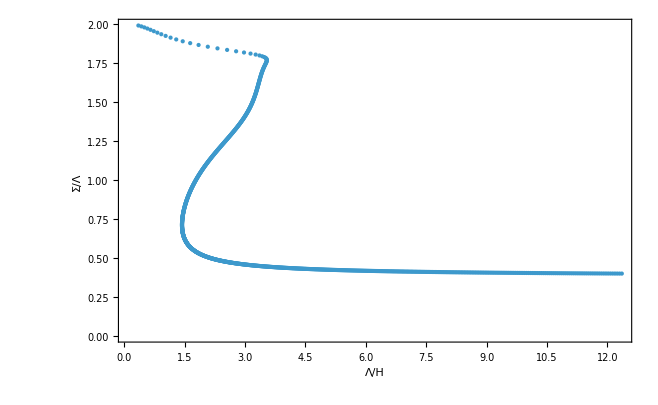

```mathematica
ListPlot[vacdata/.{ϕh_,{Λ_,a1_,phi2_,Σ_}}:> {Λ,Σ},PlotRange-> Full,Frame-> True,FrameLabel->{Λ/H,Σ/Λ}]
```

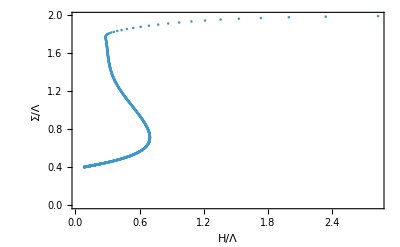

```mathematica
ListPlot[vacdata/.{ϕh_,{Λ_,a1_,phi2_,Σ_}}:> {1/Λ,Σ},PlotRange-> Full,Frame-> True,FrameLabel->{H/Λ,Σ/Λ}]
```

```mathematica
(*Expression for energy density*)
```

```mathematica
sαβ={α-> 0,β->-1/4/ϕM^2};
Edd=-1/2 H^2 α Λ^2+1/48 (9 H^4+24 H^2 Λ^2+(4-48 β) Λ^4+6 Λ^2 a[1]^2)-1/2 Λ phi[2];
```

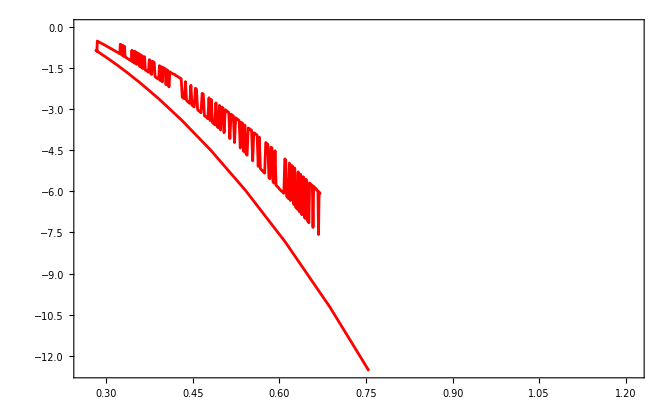

```mathematica
ListPlot[Table[{1/vacdata[[iv,2,1]],Edd/Λ^4/.{Λ->vacdata[[iv,2,1]],a[1]-> vacdata[[iv,2,2]],phi[2]-> vacdata[[iv,2,3]]}/.sαβ/.smodel},{iv,7,344}],Joined->True,Frame-> True,PlotStyle->{Red,AbsoluteThickness[2]}]
```

## HP extraction Output: Table with {ϕh, {Λ/H,a1,phi2, Σinf}}

```mathematica
Npoints=1000;
ϕHtable[i_]:= ϕEHP(1-10^(-5/100- i/Npoints 11 ))
```

```mathematica
vacdata=Table[{ϕHtable[i],gVacuaParamHP[ϕHtable[i],ϵ1,ϵ0]},{i,0,Npoints}];
```

```mathematica
(*Export["HP"<>fileVacdata,vacdata];*)
```

```mathematica
"HP"<>fileVacdata
```

HPvd_phiM_0.62_ϕQ_10_e0_6_e1_5_dat.m

```mathematica
Npoints=1000;
ϕHtable[i_]:= ϕEHP(1-10^(-5/100- i/Npoints 11 ))
```

```mathematica
ϕHtable[300]-1957637137999722/10^(15)
```

0.207278126929810612513065459024426367393839177094

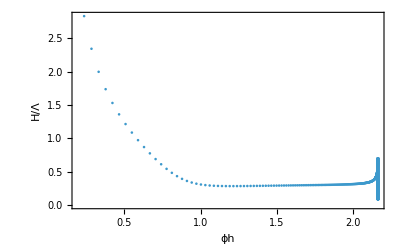

```mathematica
ListPlot[vacdata/.{ϕh_,{Λ_,a1_,phi2_,Σ_}}:> {ϕh,1/Λ},PlotRange-> Full,Frame-> True,FrameLabel->{ϕh,H/Λ}]
```

```mathematica
(*Expression for energy density*)
```

```mathematica
sαβ={α-> 0,β->-1/4/ϕM^2};
Edd=-1/2 H^2 α Λ^2+1/48 (9 H^4+24 H^2 Λ^2+(4-48 β) Λ^4+6 Λ^2 a[1]^2)-1/2 Λ phi[2];
```

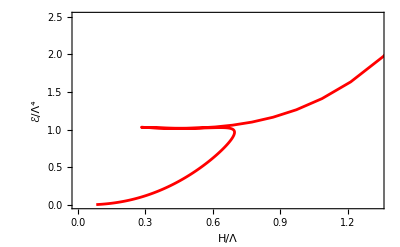

```mathematica
ListPlot[Table[{1/vacdata[[iv,2,1]],Edd/Λ^4/.{Λ->vacdata[[iv,2,1]],a[1]-> vacdata[[iv,2,2]],phi[2]-> vacdata[[iv,2,3]]}/.sαβ/.smodel},{iv,1,Npoints}],Joined->True,Frame-> True,PlotStyle->{Red,AbsoluteThickness[2]},FrameLabel-> {"H/Λ","ℰ/Λ^4"}]
```

```mathematica
smodel
```

{ϕM→31/50,ϕQI→1/10,H→1}

```mathematica
pltdata=Table[{1/vacdata[[iv,2,1]],Edd/Λ^4/.{Λ->vacdata[[iv,2,1]],a[1]-> vacdata[[iv,2,2]],phi[2]-> vacdata[[iv,2,3]]}/.sαβ/.smodel},{iv,1,Npoints}];
```

```mathematica
(*Export["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Data files/EHplot_phiM062.dat",pltdata];*)
```